```mathematica
SetCoordinates[Cartesian[x,y,z]];
```

```mathematica
V[x_]=0.3*Erfc[(20000*(x-0.00025))]-0.3
```

-0.3+0.3 Erfc[20000 (-0.00025+x)]

```mathematica
Plot[V[x],{x,-0.00,0.0005}];
```

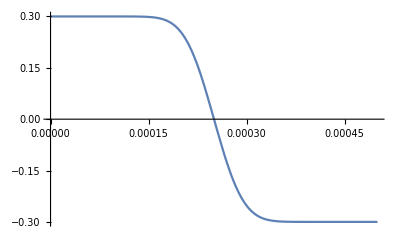

```mathematica
%5
```

```mathematica
dope=-(1/q)*Div[eps*Grad[V[x],{x,y,z}],{x,y,z}]-(ni*Exp[-V[x]/vt]-ni*Exp[V[x]/vt])
```

-ⅇ^((0.3-0.3 Erfc[20000 (-0.00025+x)])/vt) ni+ⅇ^((-0.3+0.3 Erfc[20000 (-0.00025+x)])/vt) ni-(5.41622×10^12 ⅇ^(-400000000 (-0.00025+x)^2) eps (-0.00025+x))/q

```mathematica
dopeconc=Simplify[dope/.ni->1.25*10^10/.q->1.602*10^(-19)/.eps->1.044720*10^(-12)/.vt->0.025855]
```

-1.36805×10^15 ⅇ^(-11.6032 Erfc[-5.+20000. x])+114213. ⅇ^(11.6032 Erfc[-5.+20000. x])+ⅇ^(-4.×10^8 (-0.00025+x)^2) (8.83026×10^15-3.53211×10^19 x)

```mathematica
Plot[dopeconc,{x,0,5*10^(-4)}];
```

```mathematica
%20
```

-Graphics-

```mathematica
CForm[dopeconc]
```

-1.3680544484358358e15/Power(E,11.603171533552503*Erfc(-5. + 20000.*x)) + 114213.2903983817*Power(E,11.603171533552503*Erfc(-5. + 20000.*x)) + 
   (8.830264295490818e15 - 3.5321057181963272e19*x)/Power(E,4.e8*Power(-0.00025 + x,2))

```mathematica
dopeconc/.x->0
```

1.36805×10^15